```mathematica
mystyle={FontFamily->"Times",Italic,FontSize->15};
Off[NDSolve::"ndsz"]
xmin=10^-4 ;xend=25;
insl=0.50604324925;
s=NDSolve[{ψ''[x]+2 x^-1 ψ'[x]-2 x^-2 ψ[x]-(ψ[x]^2-1)ψ[x]==0,ψ[xmin]==xmin*insl,ψ'[xmin]==insl},ψ,{x,xmin,xend},PrecisionGoal->16];
Ψ[z_]=ψ[z]/.s[[1]];
xmax=18;
tab=Table[{z,Ψ[z]},{z,xmin,xmax,(xmax-xmin)/100.}];
fit=FindFit[tab,a Tanh[b z]+c Tanh[d z]+0*e Tanh[f z],{a,b,c,d,e,f},z];
 aa=fit[[1,2]];bb=fit[[2,2]];cc=fit[[3,2]];dd=fit[[4,2]];ee=fit[[5,2]];ff=fit[[6,2]];
(* Semianalytic approximation by means of Tanh functions *)
Φ[r_]=aa Tanh[bb r]+cc Tanh[dd r]+0*ee Tanh[ff r];(* Including more terms does not improve the performance *)

(* Eq A1 *) 
eq1=K22[t,r](2K[t,r]-3K22[t,r])-(2 Derivative[0,2][B][t,r])/(A[t,r]^2 B[t,r])-(Derivative[0,1][B][t,r])^2/(A[t,r]^2 B[t,r]^2)+(2 Derivative[0,1][A][t,r] Derivative[0,1][B][t,r])/(A[t,r]^3 B[t,r])-(6 Derivative[0,1][B][t,r])/(r A[t,r]^2 B[t,r])+(2 Derivative[0,1][A][t,r])/(r A[t,r]^3)-1/(r^2 A[t,r]^2)+1/(r^2 B[t,r]^2)==η^2(1/2(Derivative[1,0][ϕ][t,r])^2+(Derivative[0,1][ϕ][t,r])^2/(2 A[t,r]^2)+ϕ[t,r]^2/(B[t,r]^2 r^2)+1/4(ϕ[t,r]^2-1)^2+ρ[t,r]/(1-v[t,r]^2));
(* Eq. A2 *) eq2=D[K22[t,r], r]+((Derivative[0,1][B][t,r])/B[t,r]+1/r)(3K22[t,r]-K[t,r])==η^2/2(Derivative[1,0][ϕ][t,r]Derivative[0,1][ϕ][t,r]-v[t,r]/(1-v[t,r]^2)A[t,r]ρ[t,r]);
(* Eq. A3 *) eq3=D[K[t,r], t]-(K[t,r]-2K22[t,r])^2-2 K22[t,r]^2==η^2((Derivative[1,0][ϕ][t,r])^2-1/4(ϕ[t,r]^2-1)^2+1/2(1+v[t,r]^2)/(1-v[t,r]^2)ρ[t,r]);
(* Eq. A4c  eq4a=K11[t,r]==K[t,r]-2K22[t,r];*)
(* Eq. A4a *) eq4b=Derivative[1,0][A][t,r]==-A[t,r](K[t,r]-2K22[t,r]);
(* Eq. A4b *) eq4c=Derivative[1,0][B][t,r]==-B[t,r]K22[t,r];
(* Eq. A5 *) eq5=(Derivative[1,0][v][t,r])/v[t,r]==(v[t,r]^2-1)(Derivative[1,0][A][t,r])/A[t,r]-(Derivative[0,1][v][t,r])/A[t,r];
(* Eq. A6 for vdot, ρ given by A1 *) eq6=(Derivative[1,0][ρ][t,r])/ρ[t,r]==(Derivative[1,0][v][t,r])/v[t,r]-2(Derivative[1,0][B][t,r])/B[t,r]-v[t,r]/A[t,r](Derivative[0,1][ρ][t,r])/ρ[t,r]-2 v[t,r]/A[t,r](Derivative[0,1][B][t,r])/B[t,r]-2 v[t,r]/(r A[t,r]);
(* Eq. A7 *) eq7=Derivative[2,0][ϕ][t,r]-K[t,r] Derivative[1,0][ϕ][t,r]-(Derivative[0,2][ϕ][t,r])/A[t,r]^2-(-(Derivative[0,1][A][t,r])/A[t,r]+(2 Derivative[0,1][B][t,r])/B[t,r]+2/r)(Derivative[0,1][ϕ][t,r])/A[t,r]^2+(2ϕ[t,r])/(B[t,r]^2 r^2)+ϕ[t,r](ϕ[t,r]^2-1)==0;
```

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at x == 22.3775.

```mathematica
(* Solution with η=0.1 *)
```

```mathematica
η=0.6  √(8π);
fraction=18;
V0=1/4;ρ0=1/4 fraction;
t0=√(16/(3 fraction η^2));
icond4a=A[t0,r]==1; (* normalized A *)
icond4b=B[t0,r]==1; (* normalized A *)
icond5=ϕ[t0,r]==Φ[r];
icond6=Derivative[1,0][ϕ][t0,r]==0;
icond8a=K22[t0,r]==-η/(√3)√(ρ0+1/4(Φ[r]^2-1)^2+Φ[r]^2/r^2+1/2 Φ'[r]^2);
icond8b=K[t0,r]==-(3η)/(√3)√(ρ0+1/4(Φ[r]^2-1)^2+Φ[r]^2/r^2+1/2 Φ'[r]^2);
icond9=ρ[t0,r]==ρ0;
icond10=v[t0,r]==10^-12;
(* Boundary conditions *)
bc1=ϕ[t,rmin]==Φ[rmin];
bc2=Derivative[0,1][ϕ][t,rmin]==Φ'[rmin];
bc4=K[t,rmin]==3K22[t,rmin];
```

```mathematica
Ztmax=0*620(* for η=7.5×10^-4 *)+0*270(* for η=2×10^-3 *)+0*130(* for η=4×10^-3 *)+0*70(* for η=7.5×10^-3 *)+0*50(* for η=0.01 *)+1*26(* for η=0.3 *);
tmax=t0+Ztmax;
Zrmin=10^-4;rmin=Zrmin ;
Zrmax=50;rmax=Zrmax;
Timing[solution=NDSolve[{eq2,eq3,eq4b,eq4c,eq5,eq6,eq7,icond4a,icond4b,icond5,icond6,icond8a,icond8b,icond9,icond10},{K,K22,A,B,ρ,ϕ,v},{t,t0,tmax},{r,rmin,rmax},AccuracyGoal->5,PrecisionGoal->5,MaxStepSize->{Automatic,Automatic}]]
```

NDSolve::pdord: Some of the functions have zero differential order so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: An insufficient number of boundary conditions have been specified for the direction of independent variable r. Artificial boundary effects may be present in the solution.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, it is recommended that you give initial conditions for all dependent variables and their derivatives.

NDSolve::eerr: Warning: Scaled local spatial error estimate of 6.5658×10^6 at t = 7.67644 in the direction of independent variable r is much greater than prescribed error tolerance. Grid spacing with 369 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

{15.172,{{K→InterpolatingFunction[{{0.180964,7.67644},{0.0001,50.}},<>],K22→InterpolatingFunction[{{0.180964,7.67644},{0.0001,50.}},<>],A→InterpolatingFunction[{{0.180964,7.67644},{0.0001,50.}},<>],B→InterpolatingFunction[{{0.180964,7.67644},{0.0001,50.}},<>],ρ→InterpolatingFunction[{{0.180964,7.67644},{0.0001,50.}},<>],ϕ→InterpolatingFunction[{{0.180964,7.67644},{0.0001,50.}},<>],v→InterpolatingFunction[{{0.180964,7.67644},{0.0001,50.}},<>]}}}

```mathematica
(* Define present time *)
```

```mathematica
ol=0.73;
rat=(1-ol)/(4 ol); (* set value for Omega_Lambda and dtermine ratio of energy densities at present *)
sol:=Sqrt[ol];
Clear[ff,amon0,bmon0,amon0n,bmon0n,alcdm,alcdmn];
ff[Zt1_]:=Part[ρ[t0+Zt,0]/.solution  /. Zt->Zt1,1];
tp1=FindRoot[ff[tt] == rat,{tt,1}][[1,2]];  (* determine present time in monopole case using the density ratio  *)
tp=t0+tp1  (* this is the actual present time *)
```

0.939018

```mathematica
(* Check Hamiltonian constraint up to tp *)
```

```mathematica
(* Lefthand side and righthand side or the Hamiltonian constraint *)
```

```mathematica
lhsHam[t_,r_]=K22[t,r](2K[t,r]-3K22[t,r])-(2 Derivative[0,2][B][t,r])/(A[t,r]^2 B[t,r])-(Derivative[0,1][B][t,r])^2/(A[t,r]^2 B[t,r]^2)+(2 Derivative[0,1][A][t,r] Derivative[0,1][B][t,r])/(A[t,r]^3 B[t,r])-(6 Derivative[0,1][B][t,r])/(r A[t,r]^2 B[t,r])+(2 Derivative[0,1][A][t,r])/(r A[t,r]^3)-1/(r^2 A[t,r]^2)+1/(r^2 B[t,r]^2);
rhsHam[t_,r_]=η^2(1/2(Derivative[1,0][ϕ][t,r])^2+(Derivative[0,1][ϕ][t,r])^2/(2 A[t,r]^2)+ϕ[t,r]^2/(B[t,r]^2 r^2)+1/4(ϕ[t,r]^2-1)^2+ρ[t,r]/(1-v[t,r]^2));
```

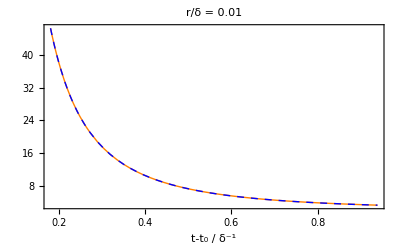
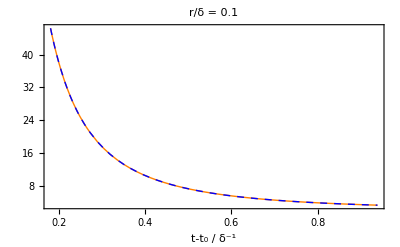
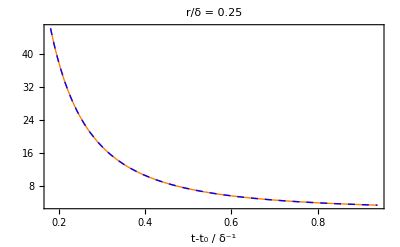
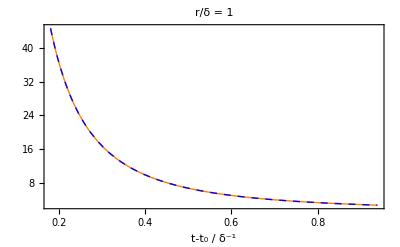
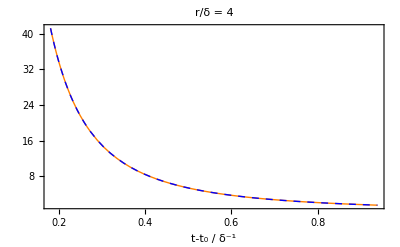
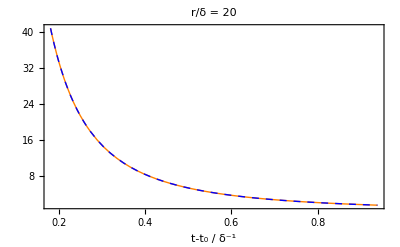

```mathematica
Plot[{lhsHam[t,#]/.solution,rhsHam[t,#]/.solution},{t,t0,tp},Frame->True,Axes->False,PlotRange->All,FrameLabel->{"t-t_0 / δ^-1",""},PlotLabel->"r/δ = "<>ToString[#],PlotStyle->{Orange,{Blue,Dashed}}]&/@{0.01,0.1,0.25,1,4,20}
```

```mathematica
(* % difference between lefthand side and righthand side in the Hamiltonian constraint *)
```

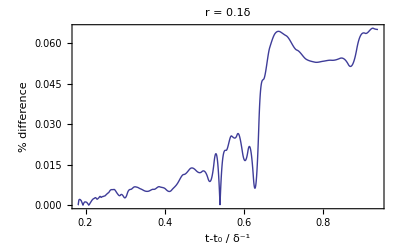
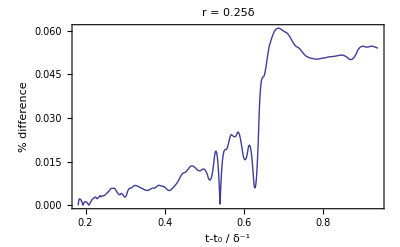
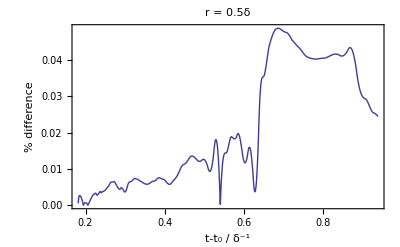
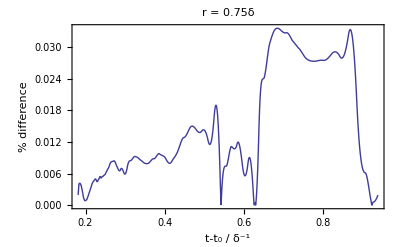
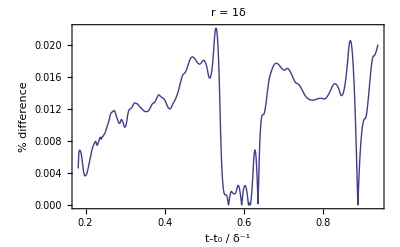
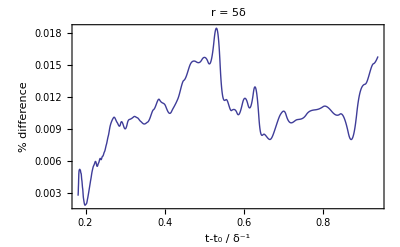

```mathematica
Plot[Abs[((lhsHam[t,#]-rhsHam[t,#])/lhsHam[t,#])/.solution]*100,{t,t0,tp},Frame->True,Axes->False,PlotRange->All,FrameLabel->{"t-t_0 / δ^-1","% difference"},PlotLabel->"r = "<>ToString[#]<>"δ"]&/@{0.1,0.25,0.5,0.75,1,5}
```

# Plots

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Figure 1b *)
```

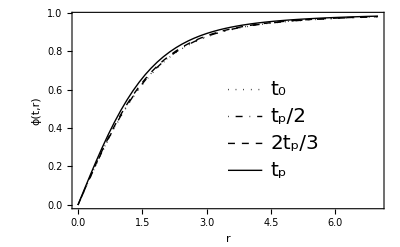

fig1b.eps

```mathematica
curves=ϕ[#,r]&/@{t0,tp/2,(2tp)/3,tp}/.solution;
plot=Plot[curves,{r,rmin,7},Frame->True,Axes->False,FrameLabel->{"r","ϕ(t,r)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{{Dotted,Black},{DotDashed,Black},{Dashed,Black},{Black,Thin}}];
(* build legend *)
styles={Dotted,DotDashed,Dashed,Thin};
times={"t_0","t_p/2","2t_p/3","t_p"};
hp=3.5;vp=0.6;sp=0.14;(* horizontal position (hp), vertical position (vp), separation (sp) *)
lgd=Graphics[Table[{Directive[styles[[i1]]],Text[Style[times[[i1]],20],{hp+1,vp-sp(i1-1)},{-1,0}],Line[{{hp,vp-sp(i1-1)},{hp+0.8,vp-sp(i1-1)}}]},{i1,1,Length[styles]}]];
Show[plot,lgd]
Export["fig1b.eps",Show[plot,lgd]]
```

```mathematica
(* Figure 2 *)
```

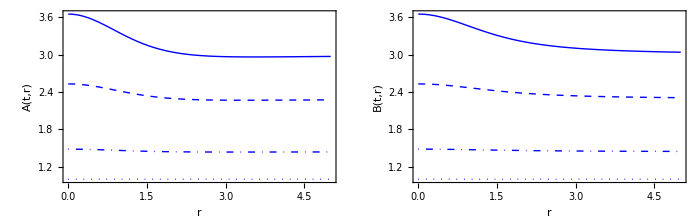

```mathematica
Clear[curvesA,curvesB]
curvesA=A[#,r]&/@{t0,tp/3,(2tp)/3,4 tp/4}/.solution;
curvesB=B[#,r]&/@{t0,tp/3,(2tp)/3,4 tp/4}/.solution;
p1=Plot[curvesA,{r,rmin,5},Frame->True,Axes->False,FrameLabel->{"r","A(t,r)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{{Thick,Dotted,Blue},{DotDashed,Blue},{Dashed,Blue},{Blue,Thin}}];
p2=Plot[curvesB,{r,rmin,5},Frame->True,Axes->False,FrameLabel->{"r","B(t,r)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{{Thick,Dotted,Blue},{DotDashed,Blue},{Dashed,Blue},{Blue,Thin}}];
Show[GraphicsGrid[{{p1,p2}},Spacings->0],ImageSize->700]
```

```mathematica
(* Import plots with η=0.1 *)
```

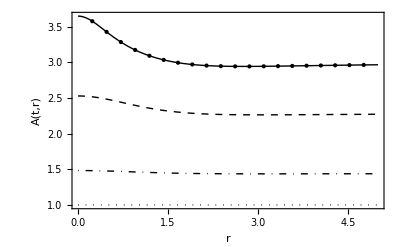
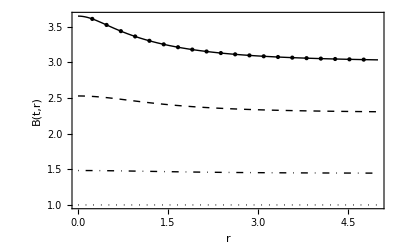
```mathematica
pp1=-Graphics-;pp2=-Graphics-;
```

fig2a.eps

fig2b.eps

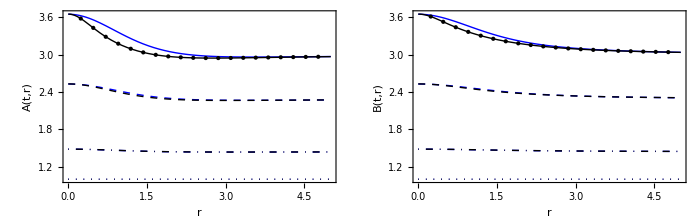

```mathematica
Export["fig2a.eps",Show[p1,pp1]]
Export["fig2b.eps",Show[p2,pp2]]
Show[GraphicsGrid[{{Show[p1,pp1],Show[p2,pp2]}},Spacings->0],ImageSize->700]
```